```mathematica
ToBaseEncode=Function[{geneExpression},
StringJoin[Flatten[IntegerDigits[#,4,4]&/@ToCharacterCode[geneExpression]]/.{0->"A",1->"T",2->"C",3->"G"}]
];

FromBaseEncode=Function[{geneExpression},
FromCharacterCode/@(FromDigits[#,4]&/@Partition[Characters[geneExpression],4]/.{"A"->0,"T"->1,"C"->2,"G"->3})
];

geneHead=Function[{gene},
Block[{
geneTail=Reverse[TakeWhile[Reverse[gene],MemberQ[setTerm,#]&]]
},
gene⟦1;;Length[gene]-Length[geneTail]⟧
]
];

geneTail=Function[{gene},
Reverse[TakeWhile[Reverse[gene],MemberQ[setTerm,#]&]]
];

mutateExpression=Function[{geneExpression},
Join[
ReplacePart[geneHead[geneExpression],RandomInteger[{1,Length[geneHead[geneExpression]]}]->RandomChoice[Join[setFunc,setTerm]]],
geneTail[geneExpression]
]
];
```

```mathematica
(* define syntax *)
(* Input *)
(* functions *)
setFunc={"Q","+","-","/","*"};

functionReturn=Function[{function,arg},Which[function=="Q",Sqrt@@arg,function=="+",Plus@@arg,function=="-",Subtract@@arg,function=="/",Divide@@arg,function=="*",Times@@arg]];

(* number of arguments for each function *)
numberArg=Function[{base},
Which[
MemberQ[setTerm,base],0,
base=="Q",1,
base=="+",2,
base=="-",2,
base=="/",2,
base=="*",2
]
];

(* terminals *)
setTerm={"a","b"};
```

```mathematica
generateGeneHead=Function[{lengthGeneHead},
(*Block[{
i=1,
geneHeadInt=First@Last@Reap[
Do[
Sow@
RandomChoice[{RandomChoice[setFunc],RandomChoice[setTerm]}],
lengthGeneHead
]
]
},
While[
MemberQ[setTerm,geneHeadInt⟦i⟧]==True,
i++
];
geneHeadInt⟦i;;-1⟧
]*)
ReplacePart[
First@Last@Reap[
Do[
Sow@
RandomChoice[{RandomChoice[setFunc],RandomChoice[setTerm]}],
lengthGeneHead
]
],1->RandomChoice[setFunc]
]
];

generateGeneTail=Function[{generateGeneHead},
Block[{lengthTail=(Length[generateGeneHead](Length[setTerm]-1)+1)},
RandomChoice[setTerm,lengthTail]
]
];

generateRandomGene=Function[{lengthGeneHead},
Block[{
geneHead=generateGeneHead[lengthGeneHead]
},
Join[
geneHead,
generateGeneTail[geneHead,setTerm]
]
]
];
```

```mathematica
KExpressionTree=Function[{gene},
Module[{
expression={},
expressionTree={},
index
},
AppendTo[expression,{Part[gene,1]}];
While[Total[numberArg/@expression⟦-1⟧]>0,
AppendTo[
expression,
Part[
Drop[gene,Total[Map[Length,expression,{1}]]],
Range@Total[numberArg/@expression⟦-1⟧]
]
]
];

Block[{subLengths=Length/@expression},
For[
i=2;index={Range[1,subLengths⟦1⟧]},
Length[index]<Length[expression],
i++,
AppendTo[
index,
Range[Last[Last[index]]+1,Last[Last[index]]+subLengths⟦i⟧]
]
]
];

Block[{
i=1,
j=1,
k=0
},
While[(*Length[expressionTree]<=Length[expression]*)Total[numberArg/@expression⟦i⟧]≠0,
(* returns the element(s) linked to the jth elem of level i *)
Block[{
(* returns the number of elements counted from j to (j+return)-1 of the next level linked to the jth elem. of the ith level *)
arity=numberArg[expression⟦(* ith level *)i,(* jth element *)j⟧]
},
ret=index⟦(* i+1 level *)i+1,k+1;;k+arity⟧;
k+=arity
];
With[{branch=index⟦i,j⟧->#&/@ret},
If[branch≠{},
AppendTo[expressionTree,branch]
]
];
If[Last[expressionTree]=={},Null,
If[j==Length[expression⟦i⟧],
i++;j=1;k=0,j++
]
]
]
];

Block[{
replace=Thread[
Flatten[index]->Flatten[expression]
]
},
TreePlot[
Graph[Flatten[DeleteCases[expressionTree,{}]]],
Top,
1,
VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.1],Black,Style[Text[#2,#1]/.replace,12,Bold]}&)
]
]
]
];

parseKExpression=Function[{gene},
Module[{
expression={},
expressionTree={},
index
},
AppendTo[expression,{Part[gene,1]}];
While[Total[numberArg/@expression⟦-1⟧]>0,
AppendTo[
expression,
Part[
Drop[gene,Total[Map[Length,expression,{1}]]],
Range@Total[numberArg/@expression⟦-1⟧]
]
]
];

Block[{subLengths=Length/@expression},
For[
i=2;index={Range[1,subLengths⟦1⟧]},
Length[index]<Length[expression],
i++,
AppendTo[
index,
Range[Last[Last[index]]+1,Last[Last[index]]+subLengths⟦i⟧]
]
]
];

Block[{
i=1,
j=1,
k=0
},
While[(*Length[expressionTree]<=Length[expression]*)Total[numberArg/@expression⟦i⟧]≠0,
(* returns the element(s) linked to the jth elem of level i *)
Block[{
(* returns the number of elements counted from j to (j+return)-1 of the next level linked to the jth elem. of the ith level *)
arity=numberArg[expression⟦(* ith level *)i,(* jth element *)j⟧]
},
ret=index⟦(* i+1 level *)i+1,k+1;;k+arity⟧;
k+=arity
];
With[{branch=index⟦i,j⟧->#&/@ret},
If[branch≠{},
AppendTo[expressionTree,branch]
]
];
If[Last[expressionTree]=={},Null,
If[j==Length[expression⟦i⟧],
i++;j=1;k=0,j++
]
]
]
];

Block[{sub,newTree,
replace=Thread[Flatten[index]->Flatten[expression]]
},
sub=First[First/@(Last[expressionTree])]->ToString[
FullForm[
functionReturn[
First[First/@(Last[expressionTree]/.replace)],
ToExpression/@(Last/@(Last[expressionTree]/.replace))
]
]
];
newTree=Delete[expressionTree,-1]/.sub;
While[newTree≠{},
sub=First[First/@(Last[newTree])]->ToString[
FullForm[
functionReturn[
First[First/@(Last[newTree]/.replace)],
ToExpression/@(Last/@(Last[newTree]/.replace))
]
]
];
newTree=Delete[newTree,-1]/.sub
];
ToExpression[Last[sub]]
]
]
];
```

```mathematica
gene=generateRandomGene[20]
```

{/,b,*,a,a,Q,/,b,/,a,*,*,b,b,/,/,/,*,b,/,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b}

```mathematica
Length[gene]
```

41

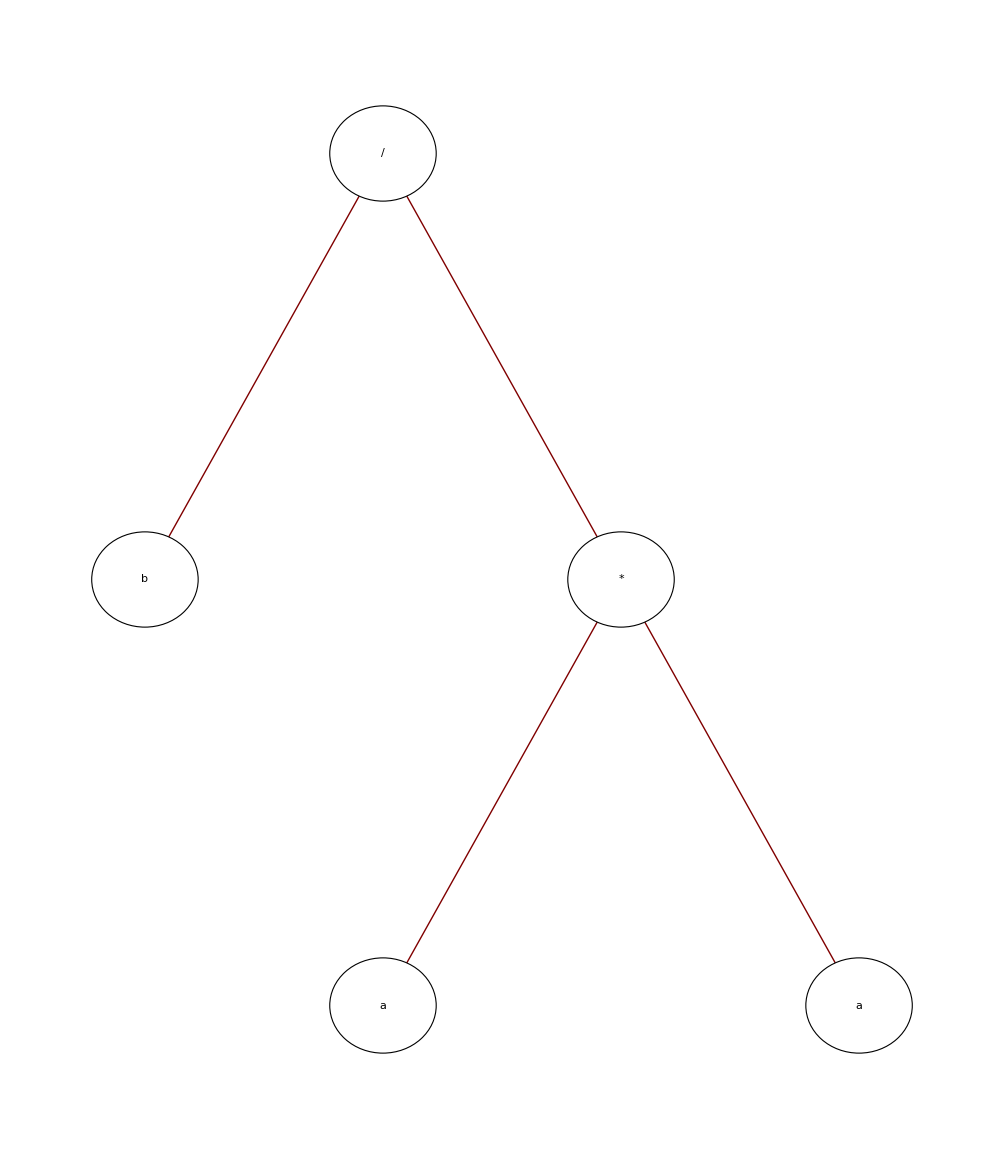

```mathematica
KExpressionTree[gene]
```

```mathematica
parseKExpression[gene]
```

b/a^2

```mathematica
test=NestList[mutateExpression,gene,100]
```

{{/,b,*,a,a,Q,/,b,/,a,*,*,b,b,/,/,/,*,b,/,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,b,/,a,-,*,b,b,/,/,/,*,b,/,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,b,/,a,-,*,b,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,*,b,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,/,b,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,/,b,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,a,/,b,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,/,/,b,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,/,/,Q,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,/,Q,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,/,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,b,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,b,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,b,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,b,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,b,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,/,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,Q,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,*,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,*,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,Q,/,+,*,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,a,a,/,+,*,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,a,/,+,*,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,-,/,+,*,a,-,-,Q,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,-,/,+,*,a,-,-,+,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,-,/,+,*,a,-,b,+,b,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,-,/,+,*,a,-,b,+,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,-,a,+,*,a,-,b,+,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,-,a,+,*,a,-,b,+,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,-,a,+,*,a,-,b,+,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,/,a,+,*,a,-,b,+,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,/,a,+,*,a,-,b,+,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,/,a,+,*,b,-,b,+,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,/,a,+,*,b,-,b,Q,*,-,/,/,*,b,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,/,a,+,*,b,-,b,Q,*,-,/,/,*,+,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,/,/,a,a,*,b,-,b,Q,*,-,/,/,*,+,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,*,/,a,a,*,b,-,b,Q,*,-,/,/,*,+,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,*,/,a,a,*,b,-,b,Q,/,-,/,/,*,+,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,*,/,a,a,*,b,-,b,Q,/,-,/,/,*,+,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,*,/,a,a,*,b,-,b,Q,/,-,/,/,*,+,*,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,*,/,a,a,*,b,-,b,Q,/,-,/,/,*,+,Q,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,*,*,a,a,*,b,-,b,Q,/,-,/,/,*,+,Q,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,*,a,a,*,b,-,b,Q,/,-,/,/,*,+,Q,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,*,a,a,*,b,-,b,Q,/,-,/,/,*,b,Q,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,*,a,a,*,b,-,b,Q,/,-,Q,/,*,b,Q,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,b,-,b,Q,/,-,Q,/,*,b,Q,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,b,-,b,Q,/,-,Q,/,*,b,-,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,b,-,b,Q,b,-,Q,/,*,b,-,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,/,-,b,Q,b,-,Q,/,*,b,-,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,/,-,b,*,b,-,Q,/,*,b,-,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,/,-,b,*,b,-,Q,/,*,b,-,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,/,-,b,*,b,-,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,/,-,b,-,b,-,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,a,*,*,-,b,-,b,-,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,a,*,*,-,b,-,b,-,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,a,*,*,-,b,-,b,-,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,a,*,*,-,b,-,b,a,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,a,*,*,b,b,-,b,a,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,a,*,-,b,b,-,b,a,Q,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,a,*,-,b,b,-,b,a,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,/,*,-,b,b,-,b,a,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,b,a,-,+,a,/,*,-,b,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,+,a,-,+,a,/,*,-,b,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,/,*,-,b,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,/,a,-,b,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,/,a,-,-,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,/,a,/,-,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,-,+,a,/,a,/,-,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,-,+,a,/,b,/,-,b,-,b,Q,a,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,-,+,a,/,b,/,-,b,-,b,Q,b,/,*,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,-,+,a,/,b,/,-,b,-,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,-,+,a,/,b,/,-,b,-,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,b,*,a,-,+,a,/,b,/,-,b,-,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,/,b,/,-,b,-,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,a,-,+,a,/,b,/,-,-,-,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,*,-,+,a,/,b,/,-,-,-,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,*,-,+,a,/,b,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,*,-,+,a,/,b,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,*,-,a,a,/,b,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,a,*,*,-,a,a,/,Q,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,a,a,/,Q,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,a,a,/,a,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,a,a,/,a,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,-,a,/,a,/,-,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,-,a,/,a,/,/,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,-,a,/,a,/,Q,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,*,a,/,a,/,Q,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,*,-,/,a,/,Q,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,*,-,/,a,/,Q,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,*,-,/,a,+,Q,-,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,*,-,/,a,+,Q,+,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,*,*,-,*,-,/,+,+,Q,+,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,+,*,-,*,-,/,+,+,Q,+,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,+,*,+,*,-,/,+,+,Q,+,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,+,*,+,*,-,/,-,+,Q,+,+,b,Q,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,+,*,+,*,-,/,-,+,Q,+,+,b,/,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,/,*,+,*,-,/,-,+,Q,+,+,b,/,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,/,*,+,*,Q,/,-,+,Q,+,+,b,/,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,-,*,+,*,Q,/,-,+,Q,+,+,b,/,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b},{/,Q,-,*,/,*,Q,/,-,+,Q,+,+,b,/,b,/,a,b,b,a,b,a,b,a,b,b,b,a,a,b,b,a,a,a,a,a,a,b,b,b}}

```mathematica
EditDistance[test⟦1⟧,#]&/@test
```

{0,1,2,3,4,4,4,4,5,5,5,5,6,6,6,6,6,6,7,7,7,7,8,9,9,9,9,10,11,11,11,10,10,9,9,10,10,11,10,10,11,11,12,12,11,12,12,12,12,12,12,12,12,12,11,12,12,12,12,13,13,13,13,13,12,11,11,11,10,10,10,11,11,11,12,12,13,13,13,12,13,13,13,13,14,14,14,14,14,14,14,14,15,15,15,15,14,14,13,13,13}

```mathematica
parseKExpression/@test
```

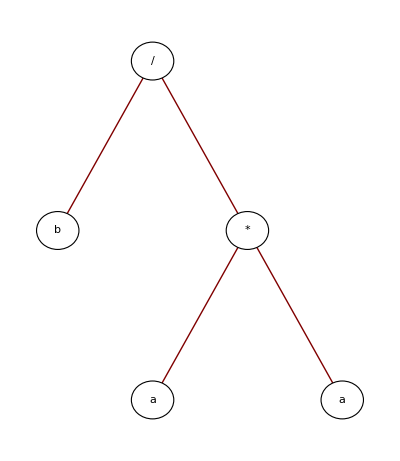
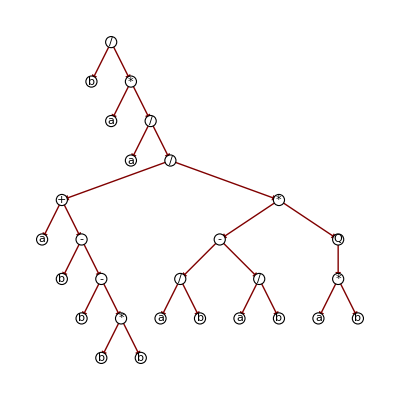
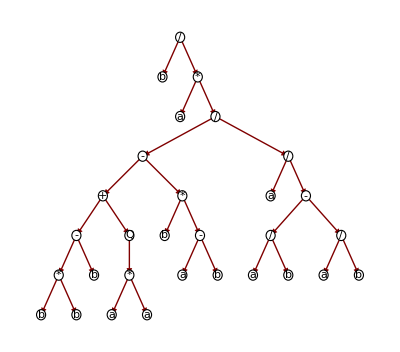
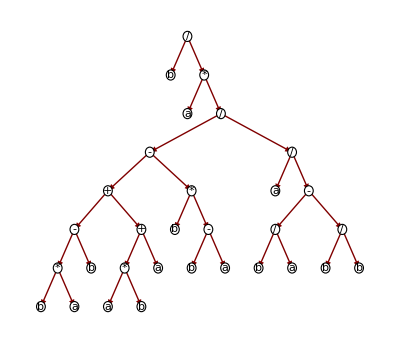
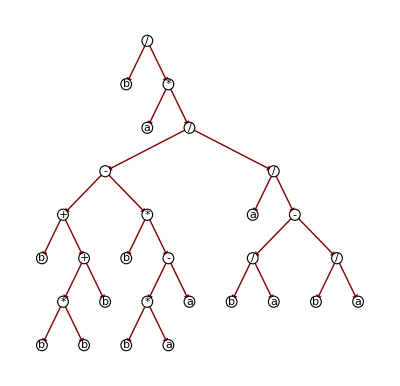
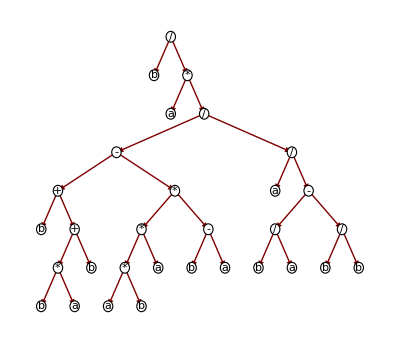
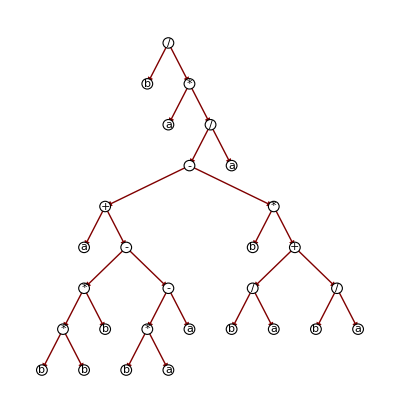
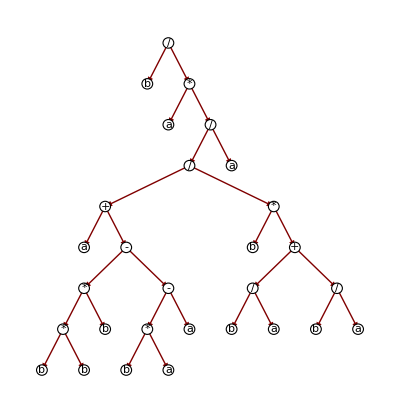
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KExpressionTree/@test
```